```mathematica
Quit
```

```mathematica
<<MBokeh`
<<CompiledFunctionTools`
If[True,  MBokehStartWebDriver["Headless"->False]];
```

### InteractiveImage

```mathematica
Quit
```

```mathematica
xr={-3,3}; yr={-2,2};
isize={400,400};

myplot[x0_, x1_, y0_, y1_, w_, h_]:=
	Module[{},
	Plot3D[Sin[x+y^2],{x,x0,x1},{y,y0,y1},ImageSize->{w,h},Boxed->False,AspectRatio->Automatic,Axes->False]
]

p=figure["title"->None, "x_range"->xr, "y_range"->yr, "plot_height"->isize[[1]], "plot_width"->isize[[2]],"tools"->Default];

(AbsoluteTiming[im=InteractiveImage[p,myplot,"reset"->True]])
```

{2.78816,Figure[<⋯>]}

```mathematica
show[p, ImageSize->isize]
```

-Graphics-

```mathematica
xr={0,6}; yr={0,6};
isize={400,400};

myplot[x0_, x1_, y0_, y1_, w_, h_]:=
	Module[{},
	DensityPlot[Sin[x+Cos[y]],{x,x0,x1},{y,y0,y1},ImageSize->{w,h},AspectRatio->Automatic, Frame->None,Axes->False,PlotRangePadding->0]
]

p=figure["title"->None, "x_range"->xr, "y_range"->yr, "plot_height"->isize[[1]], "plot_width"->isize[[2]],"tools"->Default];

(AbsoluteTiming[im=InteractiveImage[p,myplot,"reset"->True]])
```

{1.54286,Figure[<⋯>]}

```mathematica
$ResetInteractiveImage/@{"w","h"}
```

{400,400}

```mathematica
show[p, ImageSize->isize]
```

-Graphics-

```mathematica
($ResetInteractiveImage//ByteCount)/1024.^2
```

3.6632

```mathematica
$ResetInteractiveImage//Keys
```

{w,h,image,xmin,ymin,width,height}

```mathematica
AbsoluteTiming[en=encode64=ExportString[ExportString[$ResetInteractiveImage["image"],"UnsignedInteger32"],{"Base64","String"},CharacterEncoding->"UTF8"];]
```

{0.355043,Null}

```mathematica
(en//ByteCount)/1024.^2
```

0.824577

```mathematica
xr={0,6}; yr={0,6};
isize={200,350};

myplot[x0_, x1_, y0_, y1_, w_, h_]:=
	Module[{},
	Image[({{({{0}, {0.6}, {0}}), ({{0.4}, {0.1}, {0.8}}), ({{0.7}, {0.9}, {0.7}})}, {({{1}, {0}, {0.9}}), ({{0.6}, {0.6}, {1}}), ({{1}, {0.8}, {0.3}})}}),ColorSpace->"RGB"]
]

p=figure["title"->None, "x_range"->xr, "y_range"->yr, "plot_height"->isize[[1]], "plot_width"->isize[[2]],"tools"->Default];

(AbsoluteTiming[im=InteractiveImage[p,myplot,"reset"->True]])
```

{0.686133,Figure[<⋯>]}

```mathematica
$ResetInteractiveImage[#]& /@ {"w", "h"}
```

{350,200}

```mathematica
show[p, ImageSize->Reverse@isize]
```

-Graphics-

```mathematica
MandelbrotSetPlot[{}, Frame->None,Axes->False]//PlotRange
```

{{-2.,0.6},{-1.3,1.3}}

```mathematica
xr={-2,0.6}; yr={-1.3,1.3};
isize={350,350};

myplot[x0_, x1_, y0_, y1_, w_, h_]:=
	Module[{},
	MandelbrotSetPlot[{x0+y0 I, x1+y1 I}, Frame->None,Axes->False, ColorFunction->"GreenPinkTones",PlotRangePadding->0]
]

p=figure["title"->None, "x_range"->xr, "y_range"->yr, "plot_height"->isize[[1]], "plot_width"->isize[[2]],"tools"->Default];

(AbsoluteTiming[im=InteractiveImage[p,myplot,"reset"->True]])
```

{2.47721,Figure[<⋯>]}

```mathematica
$ResetInteractiveImage[#]& /@ {"w", "h"}
```

{350,350}

```mathematica
show[p, ImageSize->isize]
```

C:\Users\ulises.cervantes\AppData\Local\Temp\mbokeh.html

```mathematica
xr={0,6}; yr={0,4};
isize={400,300};

myplot[x0_, x1_, y0_, y1_, w_, h_]:=
	Module[{},
	Import["ExampleData/lena.tif"]
]

p=figure["title"->None, "x_range"->xr, "y_range"->yr, "plot_width"->isize[[1]], "plot_height"->isize[[2]],"tools"->Default];

(AbsoluteTiming[im=InteractiveImage[p,myplot,"reset"->True]])
```

{1.1274,Figure[<⋯>]}

```mathematica
$ResetInteractiveImage[#]& /@ {"w", "h"}
```

{400,300}

```mathematica
show[p, ImageSize->isize]
```

-Graphics-

```mathematica
p.inspect["Plot"]
```

```mathematica
f[x_,y_]:=Sin[x^2+y^2] Exp[-x^2]+Cos[x^2+y^2]

g2=Plot3D[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->50,Axes->False,Boxed->False];
```

```mathematica
Manipulate[Graphics3D[GeometricTransformation[g2[[1]],RotationMatrix[r,{0,0,1}]]],{r,-Pi/2,Pi/2,Pi/10.}]
```

Part::partd: Part specification g2⟦1⟧ is longer than depth of object.

```mathematica
xr=N[{-Pi,Pi}]; yr={0,4};
isize={400,400};

f[x_,y_]:=Sin[x^2+y^2] Exp[-x^2]+Cos[x^2+y^2]

g2=Plot3D[f[x,y],{x,-2,2},{y,-2,2},PlotPoints->50,Axes->False,Boxed->False, Axes->False];

myplot[x0_, x1_, y0_, y1_, w_, h_]:=
	Module[{r},
	r = (x0+x1)/2;
	Graphics3D[GeometricTransformation[g2[[1]],RotationMatrix[r,{0,0,1}]],Boxed->False]
]

p=figure["title"->None, "x_range"->xr, "y_range"->yr, "plot_width"->isize[[1]], "plot_height"->isize[[2]],"tools"->"xpan,reset,save"];

p.yaxis[].visible=False;

(AbsoluteTiming[im=InteractiveImage[p,myplot,"reset"->True]])
```

{3.1515,Figure[<⋯>]}

```mathematica
show[p]
```

C:\Users\ulises.cervantes\AppData\Local\Temp\mbokeh.html

### Testing

```mathematica
window[list_,{xmin_,xmax_},{ymin_,ymax_}]:=
Pick[list, Boole[xmin≤#[[1]]≤xmax && ymin≤#[[2]]≤ymax]& /@ list,1]
```

```mathematica
NN=1000000;
dataxy=RandomReal[{-10,10},{2,NN}];
dcolor=RandomReal[{0,1},{NN}];
```

```mathematica
AbsoluteTiming[data=Transpose[Append[dataxy,dcolor]];]
```

{0.0237238,Null}

```mathematica
xrange={-.4,.4};yrange={-3,3};
xdel=xrange[[2]]-xrange[[1]];
ydel=yrange[[2]]-yrange[[1]];
```

```mathematica
dataf=window[data,xrange,yrange];
```

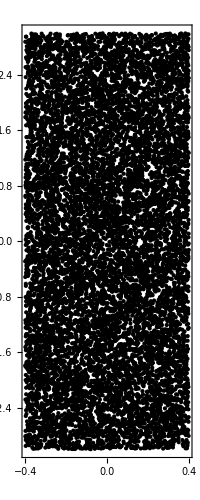

```mathematica
Graphics[Point[dataf[[All,1;;2]]],Frame->True]
```

```mathematica
xres=300;yres=300;
```

```mathematica
fquant={IntegerPart[xres (#[[1]]-xrange[[1]])/xdel]+1, IntegerPart[yres (#[[2]]-yrange[[1]])/ydel]+1, #[[3]]}&
```

{IntegerPart[(xres (#1⟦1⟧-xrange⟦1⟧))/xdel]+1,IntegerPart[(yres (#1⟦2⟧-yrange⟦1⟧))/ydel]+1,#1⟦3⟧}&

```mathematica
AbsoluteTiming[dataq=fquant/@dataf;]
```

{0.0916748,Null}

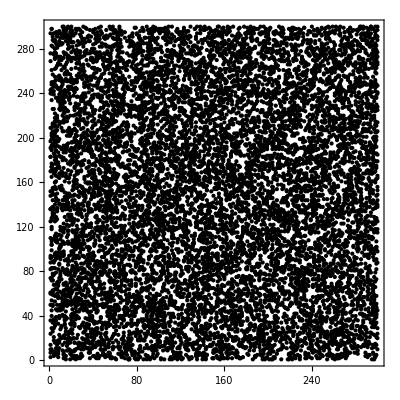

```mathematica
Graphics[Point[dataq[[All,1;;2]]],Frame->True]
```

```mathematica
AbsoluteTiming[tallyp=Partition[Flatten[Tally[dataq[[All,1;;2]]]],3];]
```

{0.0162595,Null}

```mathematica
AbsoluteTiming[tallya = Developer`ToPackedArray@Table[Table[0,xres],{yres}];]
AbsoluteTiming[carray = Developer`ToPackedArray@Table[Table[0,xres],{yres}];]
```

{0.00207289,Null}

{0.00188326,Null}

```mathematica
AbsoluteTiming[Scan[(tallya[[#[[1]],#[[2]]]]=#[[3]])&,tallyp]]
```

{0.02467,Null}

```mathematica
Select[dataq,MatchQ[#,{2,10,_}]&]//Length
```

1

```mathematica
tallya[[2,10]]
```

1

```mathematica
AbsoluteTiming[Scan[(carray[[#[[1]],#[[2]]]]=(#[[3]]/tallya[[#[[1]],#[[2]]]]))&, dataq]]
```

{0.0519012,Null}

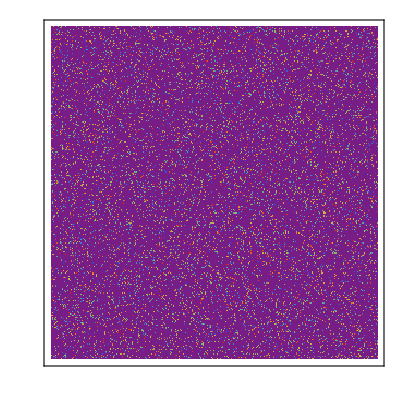

```mathematica
ArrayPlot[carray,Frame->True,ColorFunction->"Rainbow"]
```

### Implementation 2

```mathematica
Quit
```

```mathematica
datashaderC2=Compile[{{list,_Real,2}, {xrange,_Real,1}, {yrange,_Real,1},{xres,_Integer},{ yres,_Integer}},
Module[{xmin, xmax, ymin, ymax, xdel, ydel,tallya, carray,dataf, dataq, xint, yint, xr,yr},

{xmin, xmax}=xrange;
{ymin, ymax}=yrange;
xdel=xmax-xmin;
ydel=ymax-ymin;

(*tallya = ConstantArray[0,{xres,yres}];*)
carray = ConstantArray[0.,{yres,xres}];
xr=Range[xres]; yr=Range[yres];

(* filter pts in xrange x yrange *)
dataf=Pick[list, Boole[xmin≤#[[1]]<xmax && ymin≤#[[2]]<ymax]& /@ list,1];

(* Create x/y bined coordinates *)
dataq={Floor[xres (#[[1]]-xmin)/xdel]+1, Floor[yres (#[[2]]-ymin)/ydel]+1, 1.0}&/@dataf;
Scan[(
xint = Floor[#[[1]]];
yint=Floor[#[[2]]];
(* tallya[[Floor@#[[1]],Floor@#[[2]]]]++; *)
carray[[yint,xint]]=1.0
)&, dataq];

(* Final Result *)
carray
], CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
NN=500000;
dx=RandomReal[{-50,100},{NN}];
dy=RandomVariate[NormalDistribution[1,3],NN];
AbsoluteTiming[sdata=Transpose[{dx,dy}];]
```

{0.0113183,Null}

```mathematica
Last@Dimensions[sdata]
```

2

```mathematica
xr=MinMax[dx];
yr=MinMax[dy];
```

```mathematica
AbsoluteTiming[datac=Reverse@datashaderC2[sdata, xr,yr,90,30];]
```

{0.421722,Null}

```mathematica
AbsoluteTiming[datac2=AggregateData[sdata, xr,yr,90,30];]
```

{0.423374,Null}

```mathematica
datac==datac2
```

True

### Implementation 3

```mathematica
window[list_,{xmin_,xmax_},{ymin_,ymax_}]:=
Pick[list, Boole[xmin≤#[[1]]<xmax && ymin≤#[[2]]<ymax]& /@ list,1]

datashader[list_, xrange_List, yrange_List, xres_:300, yres_:300]:=
Module[{xdel, ydel, fquant,tallya,carray,dataf, dataq, tallyp},

xdel=xrange[[2]]-xrange[[1]];
ydel=yrange[[2]]-yrange[[1]];

fquant={Floor[xres (#[[1]]-xrange[[1]])/xdel]+1, Floor[yres (#[[2]]-yrange[[1]])/ydel]+1, #[[3]]}&;

tallya = Developer`ToPackedArray@Table[0,{xres},{yres}];
carray = Developer`ToPackedArray@Table[0,{xres},{yres}];

dataf=window[list,xrange,yrange];
dataq=fquant/@dataf;

tallyp=Partition[Flatten[Tally[dataq[[All,1;;2]]]],3];
Scan[(tallya[[#[[1]],#[[2]]]]=#[[3]])&,tallyp];

(* Average weighting *)
Scan[(carray[[#[[1]],#[[2]]]]+=(#[[3]]/tallya[[#[[1]],#[[2]]]]))&, dataq];
carray
]
```

```mathematica
datashaderC=Compile[{{list,_Real,2}, {xrange,_Real,1}, {yrange,_Real,1},{xres,_Integer},{ yres,_Integer}},
Module[{xmin, xmax, ymin, ymax, xdel, ydel,tallya, carray,dataf, dataq, tallyp, vmax, vmin,vtmp,xint, yint, xr,yr, col},

{xmin, xmax}=xrange;
{ymin, ymax}=yrange;
xdel=xmax-xmin;
ydel=ymax-ymin;

tallya = ConstantArray[0,{xres,yres}];
carray = ConstantArray[0.,{yres,xres}];
xr=Range[xres]; yr=Range[yres];

(* filter pts in xrange x yrange *)
dataf=Pick[list, Boole[xmin≤#[[1]]<xmax && ymin≤#[[2]]<ymax]& /@ list,1];

(* Create x/y bined coordinates *)
dataq={Floor[xres (#[[1]]-xmin)/xdel]+1, Floor[yres (#[[2]]-ymin)/ydel]+1, #[[3]]}&/@dataf;
Scan[(tallya[[Floor@#[[1]],Floor@#[[2]]]]++)&, dataq];

(* Average weighting *)
vmax = dataq[[1,3]];vmin=vmax;
Scan[(
xint = IntegerPart@Floor[#[[1]]];
yint=IntegerPart@Floor[#[[2]]];
carray[[yint,xint]]+=(#[[3]]/tallya[[xint,yint]]);
vtmp = carray[[yint,xint]];
If[vtmp>vmax, vmax=vtmp];
If[vtmp<vmin, vmin=vtmp];
)&, dataq];
vtmp = vmax-vmin;
If[vtmp ==0 && vmax==0, Return[carray]];

(* Normalize *)
Scan[(col=#;
Scan[(
If[tallya[[#,col]]>0,
If[vtmp ==0,
	carray[[col,#]] = 1.0,
	carray[[col,#]] = (carray[[col,#]]-vmin)/vtmp
]
]
)&,xr]
)&,yr];

(* Final Result *)
carray
], CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
NN=500000;
dx=RandomReal[{-50,100},{NN}];
dy=RandomVariate[NormalDistribution[1,3],NN];
dcolor = Table[1.0,{NN}];
dcolor = RandomReal[{-5,8},{NN}];
AbsoluteTiming[sdata=Transpose[{dx,dy,dcolor}];]
```

{0.0186011,Null}

```mathematica
xr=MinMax[dx];
yr=MinMax[dy];
```

```mathematica
AbsoluteTiming[datac=Reverse@datashaderC[sdata, xr,yr,90,30];]
```

{0.717773,Null}

```mathematica
Dimensions[datac]
```

{30,90}

```mathematica
AbsoluteTiming[datac2=AggregateData[sdata, xr,yr,90,30];]
```

{0.73223,Null}

```mathematica
Dimensions[datac2]
```

{30,90}

```mathematica
datac==datac2
```

True

```mathematica
MinMax[datac]
```

{0.,1.}

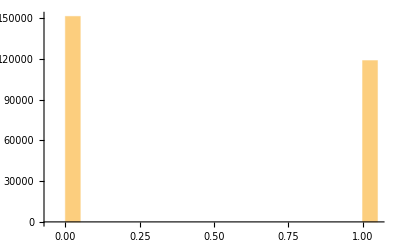

```mathematica
Histogram[Flatten[datac]]
```

```mathematica
Dimensions[ImageData[Image[datac]]]
```

{300,900}

```mathematica
cf=Function[{x},If[x==0., RGBColor[0,0,0,0],ColorData["Rainbow"][x]]]
```

Function[{x},If[x==0.,RGBColor[0, 0, 0, 0],ColorData[Rainbow][x]]]

```mathematica
AbsoluteTiming[datac=datashaderC[sdata, {0,10},{0,1},900,300];]
```

{0.961535,Null}

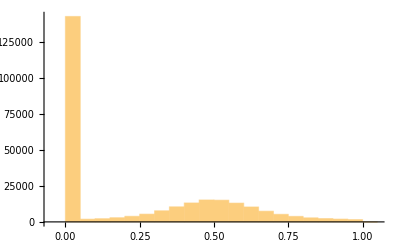

```mathematica
Histogram[Flatten[datac]]
```

```mathematica
im=Dilation[Colorize[Image[datac],ColorFunction->cf,ColorFunctionScaling->False],DiskMatrix[4]]
```

-Graphics-

```mathematica
im=Colorize[Image[Dilation[datac,DiskMatrix[2],Padding->0]],ColorFunction->cf,ColorFunctionScaling->False]
```

-Graphics-

```mathematica
p=Figure["title"->None,"x_range"->xr,"y_range"->yr,"plot_width"->900,"plot_height"->300,"tools"->"save,reset"];

p.imagergba["image"->{im},"x"->{xr[[1]]},"y"->{yr[[1]]},"dw"->{xr[[2]]-xr[[1]]},"dh"->{yr[[2]]-yr[[1]]}];
show[p]
```

C:\Users\ulises.cervantes\AppData\Local\Temp\mbokeh.html

```mathematica
datashaderC0=Compile[{{list,_Real,2},{xrange,_Real,1}, {yrange,_Real,1}, {xres,_Integer},{ yres,_Integer}},
Module[{xmin, xmax, ymin, ymax, xdel, ydel,tallya, carray,dataf, dataq, tallyp, tmp},

{xmin, xmax}=xrange;
{ymin, ymax}=yrange;
xdel=xmax-xmin;
ydel=ymax-ymin;

tallya = Developer`ToPackedArray@Table[0,{xres},{yres}];
carray = Developer`ToPackedArray@Table[0.,{xres},{yres}];

(* Create x/y bined coordinates *)
dataq={Floor[xres (#[[1]]-xmin)/xdel]+1, Floor[yres (#[[2]]-ymin)/ydel]+1, #[[3]]}&/@list;
Scan[(tallya[[Floor@#[[1]],Floor@#[[2]]]]++)&, dataq];

(* Average weighting *)
Scan[(carray[[Floor@#[[1]],Floor@#[[2]]]]=(#[[3]]/tallya[[Floor@#[[1]],Floor@#[[2]]]]))&, dataq];
carray
], CompilationTarget->"C"]

datashaderPC[list_,{xmin_,xmax_},{ymin_,ymax_}, xres_:500, yres_:500] :=
Module[{dataf, carray},
dataf=Pick[list,Boole[xmin≤#[[1]]≤xmax && ymin≤#[[2]]≤ymax]& /@ list,1];
carray = datashaderC0[dataf,{xmin, xmax}, {ymin, ymax}, xres, yres];
carray
]
```

CompiledFunction[…]

```mathematica
CompilePrint[datashaderC];
```

```mathematica
GrayLevel[1]
```

GrayLevel[1]

```mathematica
NN=10000;
dataxy=RandomReal[{-10,10},{2,NN}];
dcolor=RandomReal[{0,1},{NN}];
data=Transpose[Append[dataxy,dcolor]];
```

```mathematica
NN=1000;
dd1=Table[({x,y}=RandomReal[{-1,1},{2}];{x,y,GaussianWindow[x]GaussianWindow[y]}),{NN}];
dd2=Table[({x,y}=RandomReal[{-1,1},{2}];{x+6,y+7,GaussianWindow[x,0.3]GaussianWindow[y]}),{NN}];
dd3=Table[({x,y}=RandomReal[{-1,1},{2}];{x-3,y-8,GaussianWindow[x,0.3]GaussianWindow[y,0.8]}),{NN}];
data = Join[dd1,dd2,dd3];
```

```mathematica
ListPlot3D[data]
```

-Graphics3D-

```mathematica
ByteCount[data]/1024./1024.
```

1.14455

```mathematica
AbsoluteTiming[carray=datashader[data, {-9,9},{-9,9},50,50];]
```

{1.60765,Null}

```mathematica
AbsoluteTiming[carray=AggregateData[data, {-10,10},{-10,10},800,800];]
```

{0.0432857,Null}

```mathematica
Dimensions[carray]
```

{800,800}

```mathematica
AbsoluteTiming[ToUInteger32[carray];]
```

{0.443335,Null}

```mathematica
p=Figure["title"->None,"x_range"->{-10,10},"y_range"->{-10,10},"plot_height"->400,"plot_width"->400,"tools"->"save,reset"];

p.imagergba["image"->{UInteger32[carray]},"x"->{-10},"y"->{-10},"dw"->{20},"dh"->{20}];
```

```mathematica
show[p]
```

C:\Users\ucerv\AppData\Local\Temp\mbokeh.html

```mathematica
p.inspect[]
```

```mathematica
MinMax[carray]
```

{0.0000344091,0.0533487}

```mathematica
CompilationTarget
```

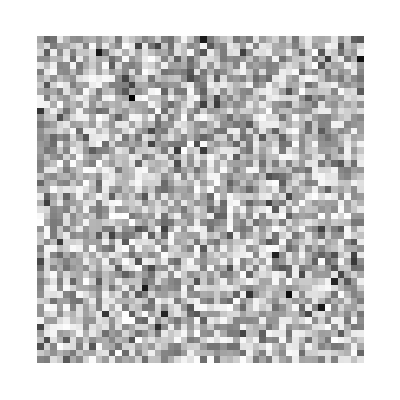

```mathematica
ArrayPlot[carray]
```

```mathematica
ToUInteger32[carray];
```

```mathematica
AbsoluteTiming[datac=datashaderC[data, {-9,9},{-9,9},25,50];]
```

{0.0777463,Null}

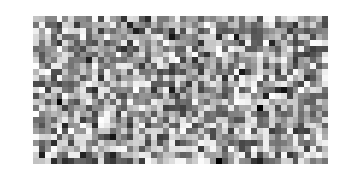

```mathematica
ArrayPlot[datac]
```

```mathematica
AbsoluteTiming[datac=datashaderPC[data, {-9,9},{-9,9},1024,1024];]
```

{0.159757,Null}

```mathematica
ArrayPlot[datac]
```

-Graphics-

```mathematica
mmax=MinMax[datac]
```

{0.,0.999981}

### touint32 1-channel

```mathematica
touint32=Quiet@Compile[{{carray, _Real, 2}, {crange,_Real,1}},
Module[{rgbarray, min, max, xdim, ydim, xrange, yrange, col, cdif, val, rgbdata,val255, rgbaval},
	{min,max}=crange;
	cdif = max-min;
	{xdim, ydim}=Dimensions[carray];
	xrange =Range[xdim];
	yrange = Range[ydim];

	rgbarray = Developer`ToPackedArray@Table[0,{xdim},{ydim}];
	val255 = Rest@IntegerDigits[255+256,2];
	If[cdif>0.,
	Scan[(col = #;
	Scan[(
	val = Rest@IntegerDigits[Floor[255 * (carray[[col,#]]-min)/cdif]+256,2];
	rgbaval = FromDigits[Join[val255,val, val, val],2];
	rgbarray[[col, #]] = rgbaval
	)&, yrange]
	)&
	,xrange], (* else not rescale *)
	Scan[(col = #;
	Scan[(
	val = Rest@IntegerDigits[Floor[255 * carray[[col,#]]]+256,2];
	rgbaval = FromDigits[Join[val255,val, val, val],2];
	rgbarray[[col, #]] = rgbaval
	)&, yrange]
	)&
	,xrange]
	];
	rgbarray
], CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
atouint32=Quiet@Compile[{{carray, _Real, 2}, {crange,_Real,1}},
Module[{rgbarray, min, max, xdim, ydim, xrange, yrange, col, cdif, val, rgbdata,val255, rgbaval},
	{min,max}=crange;
	cdif = max-min;
	{xdim, ydim}=Dimensions[carray];
	xrange =Range[xdim];
	yrange = Range[ydim];

	rgbarray = Developer`ToPackedArray@Table[0,{xdim},{ydim}];
	val255 = BitShiftLeft[255, 24];
	If[cdif>0.,
	Scan[(col = #;
	Scan[(
	val = Floor[255 * (carray[[col,#]]-min)/cdif];
	rgbaval = val255+BitShiftLeft[val,16]+BitShiftLeft[val,8]+val;
	rgbarray[[col, #]] = rgbaval
	)&, yrange]
	)&
	,xrange], (* else not rescale *)
	Scan[(col = #;
	Scan[(
	val = Floor[255 * carray[[col,#]]];
	rgbaval = val255+BitShiftLeft[val,16]+BitShiftLeft[val,8]+val;
	rgbarray[[col, #]] = rgbaval
	)&, yrange]
	)&
	,xrange]
	];
	rgbarray
], CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
For
```

```mathematica
btouint32=Quiet@Compile[{{carray, _Real, 2}, {crange,_Real,1}},
Module[{rgbarray, min, max, xdim, ydim, xrange, yrange, col, cdif, val, rgbdata,val255, rgbaval,i,j},
	{min,max}=crange;
	cdif = max-min;
	{xdim, ydim}=Dimensions[carray];

	rgbarray = Developer`ToPackedArray@Table[0,{xdim},{ydim}];
	val255 = BitShiftLeft[255, 24];
	If[cdif>0.,
	For[i=1, i≤xdim, i++,
	For[j=1, j≤ydim, j++,
	val = Floor[255 * (carray[[i,j]]-min)/cdif];
	rgbaval = val255+BitShiftLeft[val,16]+BitShiftLeft[val,8]+val;
	rgbarray[[i, j]] = rgbaval
]
], (* else not rescale *)
	Scan[(col = #;
	Scan[(
	val = Floor[255 * carray[[col,#]]];
	rgbaval = val255+BitShiftLeft[val,16]+BitShiftLeft[val,8]+val;
	rgbarray[[col, #]] = rgbaval
	)&, yrange]
	)&
	,xrange]
	];
	rgbarray
], CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
mmax=MinMax[carray]
```

{0.,1.}

```mathematica
AbsoluteTiming[arr1=touint32[carray,{0.,0.}];]
```

{0.807559,Null}

```mathematica
AbsoluteTiming[arr2=atouint32[carray,mmax];]
```

{0.436564,Null}

```mathematica
AbsoluteTiming[arr3=btouint32[carray,mmax];]
```

{0.438144,Null}

```mathematica
arr1==arr2
```

True

```mathematica
arr1===arr3
```

True

```mathematica
rgbdatac//Dimensions
```

{800,800}

```mathematica
AbsoluteTiming[rgbdatac=touint32[datac,mmax];]
```

{2.32508,Null}

```mathematica
AbsoluteTiming[mm=ToUInteger32[datac];]
```

{2.47807,Null}

```mathematica
im = Image[RandomReal[{0,.5},{1024,1024}]];
```

```mathematica
MinMax[ImageData[im]]
```

{6.87314×10^-9,0.499999}

```mathematica
AbsoluteTiming[mm=ToUInteger32[im];]
```

{2.33898,Null}

```mathematica
AbsoluteTiming[mm2=touint32[Reverse@ImageData[im], {0.,0.}];]
```

{2.3455,Null}

```mathematica
Dimensions[mm]
```

{1024,1024}

```mathematica
tt=Table[RandomReal[{0,1},{3}],{5},{6}]
```

{{{0.880135,0.575655,0.859469},{0.328167,0.231511,0.370782},{0.838902,0.812071,0.915017},{0.918204,0.0907666,0.112969},{0.0416843,0.451602,0.312688},{0.935109,0.714164,0.711984}},{{0.24568,0.16632,0.931746},{0.786699,0.712806,0.433762},{0.157803,0.608497,0.790757},{0.880043,0.105781,0.712172},{0.237278,0.348173,0.184632},{0.484202,0.365421,0.893208}},{{0.291143,0.242263,0.589037},{0.744713,0.273485,0.131205},{0.950758,0.572193,0.630583},{0.197283,0.00101047,0.853479},{0.975075,0.83015,0.893319},{0.542683,0.761777,0.715562}},{{0.475351,0.191918,0.343201},{0.783239,0.120111,0.505134},{0.515992,0.905449,0.0830579},{0.981537,0.847678,0.496788},{0.169724,0.154621,0.0533883},{0.39898,0.0144236,0.0959035}},{{0.931033,0.0476062,0.356126},{0.46165,0.910404,0.816166},{0.839061,0.203106,0.767157},{0.441603,0.874019,0.184651},{0.215237,0.643242,0.295454},{0.399739,0.568042,0.715484}}}

```mathematica
Dimensions[tt]
```

{5,6,3}

```mathematica
ArrayQ[tt]
```

True

```mathematica
mm==mm2
```

False

### touint32 - 3/4 channels

```mathematica
to3uint32=Quiet@Compile[{{carray, _Real, 3}, {crange,_Real,1}},
Module[{rgbarray, min, max, xdim, ydim, xrange, yrange, col, cdif, rval, gval, bval, rgbdata,val255, rgbaval, zdim},
	{min,max}=crange;
	cdif = max-min;
	{xdim, ydim,zdim}=Dimensions[carray];
	If[zdim=!=3, Return[-1]];
	xrange =Range[xdim];
	yrange = Range[ydim];

	rgbarray = Developer`ToPackedArray@Table[0,{xdim},{ydim}];
	val255 = Rest@IntegerDigits[255+256,2];
	If[cdif>0.,
	Scan[(col = #;
	Scan[(
	rval = Rest@IntegerDigits[Floor[255 * (carray[[col,#,1]]-min)/cdif]+256,2];
	gval = Rest@IntegerDigits[Floor[255 * (carray[[col,#,2]]-min)/cdif]+256,2];
	bval = Rest@IntegerDigits[Floor[255 * (carray[[col,#,3]]-min)/cdif]+256,2];
	rgbaval = FromDigits[Join[val255,bval, gval, rval],2];
	rgbarray[[col, #]] = rgbaval
	)&, yrange]
	)&
	,xrange], (* else not rescale *)
	Scan[(col = #;
	Scan[(
	rval = Rest@IntegerDigits[Floor[255 * carray[[col,#,1]]]+256,2];
	gval = Rest@IntegerDigits[Floor[255 * carray[[col,#,2]]]+256,2];
	bval = Rest@IntegerDigits[Floor[255 * carray[[col,#,3]]]+256,2];
	rgbaval = FromDigits[Join[val255,bval, gval, rval],2];
	rgbarray[[col, #]] = rgbaval
	)&, yrange]
	)&
	,xrange]
	];
	rgbarray
], CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
to4uint32=Quiet@Compile[{{carray, _Real, 3}, {crange,_Real,1}},
Module[{rgbarray, min, max, xdim, ydim, xrange, yrange, col, cdif, rval, gval, bval, rgbdata,aval, rgbaval, zdim},
	{min,max}=crange;
	cdif = max-min;
	{xdim, ydim,zdim}=Dimensions[carray];
	If[zdim=!=4, Return[-1]];
	xrange =Range[xdim];
	yrange = Range[ydim];

	rgbarray = Developer`ToPackedArray@Table[0,{xdim},{ydim}];
	If[cdif>0.,
	Scan[(col = #;
	Scan[(
	rval = Rest@IntegerDigits[Floor[255 * (carray[[col,#,1]]-min)/cdif]+256,2];
	gval = Rest@IntegerDigits[Floor[255 * (carray[[col,#,2]]-min)/cdif]+256,2];
	bval = Rest@IntegerDigits[Floor[255 * (carray[[col,#,3]]-min)/cdif]+256,2];
	aval = Rest@IntegerDigits[Floor[255 * (carray[[col,#,4]]-min)/cdif]+256,2];
	rgbaval = FromDigits[Join[aval,bval, gval, rval],2];
	rgbarray[[col, #]] = rgbaval
	)&, yrange]
	)&
	,xrange], (* else not rescale *)
	Scan[(col = #;
	Scan[(
	rval = Rest@IntegerDigits[Floor[255 * carray[[col,#,1]]]+256,2];
	gval = Rest@IntegerDigits[Floor[255 * carray[[col,#,2]]]+256,2];
	bval = Rest@IntegerDigits[Floor[255 * carray[[col,#,3]]]+256,2];
	aval = Rest@IntegerDigits[Floor[255 * carray[[col,#,4]]]+256,2];
	rgbaval = FromDigits[Join[aval,bval, gval, rval],2];
	rgbarray[[col, #]] = rgbaval
	)&, yrange]
	)&
	,xrange]
	];
	rgbarray
], CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
im=Import["ExampleData/lena.tif"];
```

```mathematica
AbsoluteTiming[mm=ToUInteger32[im];]
```

{0.448927,Null}

```mathematica
datac=Reverse@ImageData[im];
```

```mathematica
AbsoluteTiming[mm2=to3uint32[datac,{0.,0.}];]
```

{0.382548,Null}

```mathematica
Image
```

```mathematica
Dimensions[datac]
```

{116,150,3}

```mathematica
im=Rasterize[DensityPlot[Sin[x+Cos[y]],{x,0,2π},{y,0,2Pi},ImageSize->200, Axes->False, Frame->None], RasterSize->400];
```

```mathematica
Head[im]
```

Graphics

```mathematica
Dimensions[mm=ToUInteger32[im]]
```

{400,400}

```mathematica
ImageChannels[im]
```

3

```mathematica
mm[[1,1]]
```

4294967295

```mathematica
func=Sin[5 x+Cos[10 y]]
func=Sin[x y]
rsize=20;
ppoints=50;

xprange={x,0,10};yprange={y,0,10};
plot=DensityPlot@@{func,xprange,yprange,ImageSize->rsize,Axes->False,Frame->None,MaxRecursion->0,PlotPoints->ppoints}
im=Rasterize[plot,RasterSize->rsize];
p=Figure["title"->None,"x_range"->{0,10},"y_range"->{0,10},"plot_height"->400,"plot_width"->400,"tools"->"save,reset"];

p.imagergba["image"->{im},"x"->{0},"y"->{0},"dw"->{10},"dh"->{10}];

imgsrc=First[p.select[ColumnDataSourceClass,None]."data"];
```

Sin[5 x+Cos[10 y]]

Sin[x y]

-Graphics-

```mathematica
rt=ResetTool[]
```

ResetTool[<⋯>]

```mathematica
imgsrc.add[First[(imgsrc."data")["image"]],"oimage"]
```

oimage

```mathematica
imgsrc.inspect[]
```

Select::normal: Nonatomic expression expected at position 1 in Select[MBokeh`Private`attrs$33187,#1[type]===FE`MBokeh`Private`type$$20&].

Function::argb: Function called with 0 arguments; between 1 and 3 arguments are expected.

Select::normal: Nonatomic expression expected at position 1 in Select[MBokeh`Private`attrs$33187,#1[type]===FE`MBokeh`Private`type$$39&].

Function::argb: Function called with 0 arguments; between 1 and 3 arguments are expected.

Select::normal: Nonatomic expression expected at position 1 in Select[MBokeh`Private`attrs$33187,#1[type]===FE`MBokeh`Private`type$$53&].

Function::argb: Function called with 0 arguments; between 1 and 3 arguments are expected.

Select::normal: Nonatomic expression expected at position 1 in Select[MBokeh`Private`attrs$33187,#1[type]===FE`MBokeh`Private`type$$152&].

Function::argb: Function called with 0 arguments; between 1 and 3 arguments are expected.

Select::normal: Nonatomic expression expected at position 1 in Select[MBokeh`Private`attrs$33187,#1[type]===FE`MBokeh`Private`type$$62&].

Function::argb: Function called with 0 arguments; between 1 and 3 arguments are expected.

Select::normal: Nonatomic expression expected at position 1 in Select[MBokeh`Private`attrs$33187,#1[type]===FE`MBokeh`Private`type$$22&].

Function::argb: Function called with 0 arguments; between 1 and 3 arguments are expected.

Select::normal: Nonatomic expression expected at position 1 in Select[MBokeh`Private`attrs$33187,#1[type]===FE`MBokeh`Private`type$$25&].

Function::argb: Function called with 0 arguments; between 1 and 3 arguments are expected.

```mathematica
imgsrc."data"
```

<|image→{<|__ndarray__→5p9L/+ehTf/oo1D/6aVS/+qnVf/qqVf/66ta/+ysXP/srl7/7K9g/+yxYv/ssmX/7LNm/+yzaP/s
tGj/7LRo/+yzaP/ss2f/7LJl/+yxY//noU3/8blq//nNhP/+3pv//+uy///xu///67L//+Ce//jP
if/wvHH/2qZl/6qTff99gZT/XnGV/05mg/9KYn//TGWO/2BvmP9/eob/ropr/+ijUP/5zYT//+qu
///vuf/61pH/5bFp/6iJcP9Yao3/OF+b/1Blg/+CgIn/t6GI//HDff/704v/+9yc/9/Mof+/spr/
qJZ4/5mDdP9+eof/6aVS//7em///77n/9sZ8/6eKcf82XJT/OV+d/6qJbP/vxoP//u22//3Zk//a
pWL/WXGi/zdciv91dov/3axp//Leqf/84qT/8bps/4mEjP/qp1X//+uy//rWkf+ninH/Nl2a/3d3
jP/wwXr//+mu/+C6gf+BeHX/TWaT/5mUlP/0z4//9s6J/7CklP+HfH7/fHh0/6Woqf/1xHj/y7ud
/+qpV///8bv/5bFp/zZclP93d4z//NWP//3fn/+chHX/MFmR/9egX///7rb/7rlu/0Jimf9lcZP/
+c6F//vjqP+1jWf/L1mP/8SWZv/96bH/66ta///rsv+oiXD/OV+d//DBev/935//fnl1/2Vvhf/x
0JT/6ceO/2Ruff+RiHv/99ia/7uvmv9Za43/oaCP//nQiP+Pnaj/h32B/6qwpv/srFz//+Ce/1hq
jf+qiWz//+mu/5yEdf9lb4X//tyX/9aobf9BYIb/8caB/+XJlP9BYY//wKF8//fjrv+BeoP/eoGY
//XdpP/TnFz/UnCf/+yuXv/4z4n/OF+b/+/Gg//guoH/MFmR//HQlP/WqG3/cnaN//rZmP+RkZr/
gX+A//fanv+AiI3/qYpl//PCd/9veof/t6uP/+rAfv92gpL/7K9g//C8cf9QZYP//u22/4F4df/X
oF//6ceO/0Fghv/62Zj/uY1f/6qUev/c0K7/S2SG//LBdv++lF//gIiO/+bZrv9/eHX/6qhW/8eq
ff/ssWL/2qZl/4KAif/92ZP/TWaT///utv9kbn3/8caB/5GRmv+qlHr/77Rk/3R1g//42Jf/ZnOP
/+3Zpv92g47/yK1//62ahv+XioX/47Fu/+yyZf+qk33/t6GI/9qlYv+ZlJT/7rlu/5GIe//lyZT/
gX+A/9zQrv90dYP/2cij/2Fsff/nwYX/U2iP//C8cv9xeJP/6Lh0/7GObf/WtIH/7LNm/32BlP/x
w33/WXGi//TPj/9CYpn/99ia/0Fhj//32p7/S2SG//jYl/9hbH3/9c+M/4B4cv/4z4f/oYht/+e/
f/+7mnP/0Kt4/9Suef/ss2j/XnGV//vTi/83XIr/9s6J/2Vxk/+7r5r/wKF8/4CIjf/ywXb/ZnOP
/+fBhf+AeHL/rLOw/56Ylf+coZn/2bSB/6SVif/et33/r5Fq/+y0aP9OZoP/+9yc/3V2i/+wpJT/
+c6F/1lrjf/3467/qYpl/76UX//t2ab/U2iP//jPh/+emJX/fXqJ//bVlv8+X4f/7rpy/9Ckb/9h
coj/7LRo/0pif//fzKH/3axp/4d8fv/746j/oaCP/4F6g//zwnf/gIiO/3aDjv/wvHL/oYht/5yh
mf/21Zb/x6Z8/6+onf+2qpP/j4qP/5OVlv/ss2j/TGWO/7+ymv/y3qn/fHh0/7WNZ//50Ij/eoGY
/296h//m2a7/yK1//3F4k//nv3//2bSB/z5fh/+vqJ3/7NGX/4uEgP/Tmlb/69Gb/+yzZ/9gb5j/
qJZ4//zipP+lqKn/L1mP/4+dqP/13aT/t6uP/394df+tmob/6Lh0/7uac/+klYn/7rpy/7aqk/+L
hID/gpWq/9G1hP/Ev6f/7LJl/396hv+Zg3T/8bps//XEeP/Elmb/h32B/9OcXP/qwH7/6qhW/5eK
hf+xjm3/0Kt4/963ff/QpG//j4qP/9OaVv/RtYT/zJ5o/5ySjv/ssWP/ropr/356h/+JhIz/y7ud
//3psf+qsKb/UnCf/3aCkv/Hqn3/47Fu/9a0gf/Urnn/r5Fq/2FyiP+TlZb/69Gb/8S/p/+cko7/
oZqU/w==
,dtype→uint32,shape→{20,20}|>},x→{0},y→{0},dw→{10},dh→{10},oimage→<|__ndarray__→5p9L/+ehTf/oo1D/6aVS/+qnVf/qqVf/66ta/+ysXP/srl7/7K9g/+yxYv/ssmX/7LNm/+yzaP/s
tGj/7LRo/+yzaP/ss2f/7LJl/+yxY//noU3/8blq//nNhP/+3pv//+uy///xu///67L//+Ce//jP
if/wvHH/2qZl/6qTff99gZT/XnGV/05mg/9KYn//TGWO/2BvmP9/eob/ropr/+ijUP/5zYT//+qu
///vuf/61pH/5bFp/6iJcP9Yao3/OF+b/1Blg/+CgIn/t6GI//HDff/704v/+9yc/9/Mof+/spr/
qJZ4/5mDdP9+eof/6aVS//7em///77n/9sZ8/6eKcf82XJT/OV+d/6qJbP/vxoP//u22//3Zk//a
pWL/WXGi/zdciv91dov/3axp//Leqf/84qT/8bps/4mEjP/qp1X//+uy//rWkf+ninH/Nl2a/3d3
jP/wwXr//+mu/+C6gf+BeHX/TWaT/5mUlP/0z4//9s6J/7CklP+HfH7/fHh0/6Woqf/1xHj/y7ud
/+qpV///8bv/5bFp/zZclP93d4z//NWP//3fn/+chHX/MFmR/9egX///7rb/7rlu/0Jimf9lcZP/
+c6F//vjqP+1jWf/L1mP/8SWZv/96bH/66ta///rsv+oiXD/OV+d//DBev/935//fnl1/2Vvhf/x
0JT/6ceO/2Ruff+RiHv/99ia/7uvmv9Za43/oaCP//nQiP+Pnaj/h32B/6qwpv/srFz//+Ce/1hq
jf+qiWz//+mu/5yEdf9lb4X//tyX/9aobf9BYIb/8caB/+XJlP9BYY//wKF8//fjrv+BeoP/eoGY
//XdpP/TnFz/UnCf/+yuXv/4z4n/OF+b/+/Gg//guoH/MFmR//HQlP/WqG3/cnaN//rZmP+RkZr/
gX+A//fanv+AiI3/qYpl//PCd/9veof/t6uP/+rAfv92gpL/7K9g//C8cf9QZYP//u22/4F4df/X
oF//6ceO/0Fghv/62Zj/uY1f/6qUev/c0K7/S2SG//LBdv++lF//gIiO/+bZrv9/eHX/6qhW/8eq
ff/ssWL/2qZl/4KAif/92ZP/TWaT///utv9kbn3/8caB/5GRmv+qlHr/77Rk/3R1g//42Jf/ZnOP
/+3Zpv92g47/yK1//62ahv+XioX/47Fu/+yyZf+qk33/t6GI/9qlYv+ZlJT/7rlu/5GIe//lyZT/
gX+A/9zQrv90dYP/2cij/2Fsff/nwYX/U2iP//C8cv9xeJP/6Lh0/7GObf/WtIH/7LNm/32BlP/x
w33/WXGi//TPj/9CYpn/99ia/0Fhj//32p7/S2SG//jYl/9hbH3/9c+M/4B4cv/4z4f/oYht/+e/
f/+7mnP/0Kt4/9Suef/ss2j/XnGV//vTi/83XIr/9s6J/2Vxk/+7r5r/wKF8/4CIjf/ywXb/ZnOP
/+fBhf+AeHL/rLOw/56Ylf+coZn/2bSB/6SVif/et33/r5Fq/+y0aP9OZoP/+9yc/3V2i/+wpJT/
+c6F/1lrjf/3467/qYpl/76UX//t2ab/U2iP//jPh/+emJX/fXqJ//bVlv8+X4f/7rpy/9Ckb/9h
coj/7LRo/0pif//fzKH/3axp/4d8fv/746j/oaCP/4F6g//zwnf/gIiO/3aDjv/wvHL/oYht/5yh
mf/21Zb/x6Z8/6+onf+2qpP/j4qP/5OVlv/ss2j/TGWO/7+ymv/y3qn/fHh0/7WNZ//50Ij/eoGY
/296h//m2a7/yK1//3F4k//nv3//2bSB/z5fh/+vqJ3/7NGX/4uEgP/Tmlb/69Gb/+yzZ/9gb5j/
qJZ4//zipP+lqKn/L1mP/4+dqP/13aT/t6uP/394df+tmob/6Lh0/7uac/+klYn/7rpy/7aqk/+L
hID/gpWq/9G1hP/Ev6f/7LJl/396hv+Zg3T/8bps//XEeP/Elmb/h32B/9OcXP/qwH7/6qhW/5eK
hf+xjm3/0Kt4/963ff/QpG//j4qP/9OaVv/RtYT/zJ5o/5ySjv/ssWP/ropr/356h/+JhIz/y7ud
//3psf+qsKb/UnCf/3aCkv/Hqn3/47Fu/9a0gf/Urnn/r5Fq/2FyiP+TlZb/69Gb/8S/p/+cko7/
oZqU/w==
,dtype→uint32,shape→{20,20}|>|>

```mathematica
show[p]
```

C:\Users\ulises.cervantes\AppData\Local\Temp\mbokeh.html

```mathematica
DensityPlot
```

```mathematica
RandomReal[5,2]
```

{1.98985,3.68443}

```mathematica
Evaluate[Sum[Sin[RandomReal[10,2].{x,y}],{10}]]
```

Sin[0.204006 x+0.583041 y]+Sin[8.04849 x+1.27165 y]+Sin[2.98371 x+3.46101 y]+Sin[2.33412 x+3.85427 y]+Sin[6.60185 x+4.63668 y]+Sin[8.00341 x+5.3376 y]+Sin[3.75661 x+6.90076 y]+Sin[0.442286 x+6.92203 y]+Sin[6.25147 x+8.4602 y]+Sin[8.14901 x+9.02051 y]